```mathematica
Clear[s, invs,g,x,u, d,rs, a, b, rho,rho1,rho2,rho3, rhodash, rhodash1, rhodash2,rhodash3, lgs, lgs1,lgs2, lgs3,lgs4,lgs5,lgs6]
```

```mathematica
w = {{-g,g},{g,-g}};
```

```mathematica
Eigenvectors[w] 
evec = {{1,1},{-1,1}}
```

{{-1,1},{1,1}}

{{1,1},{-1,1}}

```mathematica
s = Transpose[{Normalize[evec[[1]]],Normalize[evec[[2]]]}]
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
invs = Simplify[Assuming[{ab>0, ba>0},Inverse[s]]];
```

```mathematica
diagw = Simplify[invs.w.s]
```

{{0,0},{0,-2 g}}

```mathematica
bcu = {{1,0},{0,Exp[u]}};
```

```mathematica
rhodash[r_] = {{1, 1/r, 0, 0},{0, 0, Exp[-Sqrt[Abs[diagw[[2,2]]]/d]r]/r,Exp[Sqrt[Abs[diagw[[2,2]]]/d]r]/r}} /.√2 √(1/d)√Abs[g]->x
```

{{1,1/r,0,0},{0,0,ⅇ^(-r x)/r,ⅇ^(r x)/r}}

```mathematica
lgs1 = Join[rhodash[rs],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];
lgs2 = Join[rhodash[a], -invs.bcu.s.rhodash[a], {{0,0,0,0},{0,0,0,0}},2];
lgs3 = Join[rhodash'[a],-rhodash'[a],{{0,0,0,0},{0,0,0,0}},2];
lgs4= Join[{{0,0,0,0},{0,0,0,0}},invs.bcu.s.rhodash[b],-rhodash[b],2];
lgs5 = Join[{{0,0,0,0},{0,0,0,0}},rhodash'[b],-rhodash'[b],2];
lgs6 = Join[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,Infinity}},2];
```

```mathematica
lgs = Join[lgs1, lgs2, lgs3, lgs4,lgs5,lgs6,1];
```

```mathematica
lgs = lgs[[1;;11,1;;11]];
```

```mathematica
c =Assuming[{ab>0, ba>0,d>0,kt>0,b>a>rs>0}, LinearSolve[lgs,Transpose[{{0,0,0,0,0,0,0,0,0,0,1}}]]];
```

```mathematica
c = Assuming[b > a > rs > 0,Simplify[c]];
```

```mathematica
c = Join[c,{{0}}];
```

```mathematica
Simplify[lgs.c[[1;;11]]]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}}

```mathematica
rhodash1[r_] = rhodash[r].c[[1;;4]];
```

```mathematica
Simplify[rhodash1[rs]]
```

{{0},{0}}

```mathematica
rhodash2[r_] = rhodash[r].c[[5;;8]];
```

```mathematica
Simplify[rhodash1[a] - invs.bcu.s.rhodash2[a]]
Simplify[rhodash1'[a] - rhodash2'[a]]
```

{{0},{0}}

{{0},{0}}

```mathematica
rhodash3[r_] = rhodash[r].c[[9;;12]];
```

```mathematica
Simplify[invs.bcu.s.rhodash2[b] - rhodash3[b]]
Simplify[rhodash2'[b] - rhodash3'[b]]
Simplify[rhodash3[Infinity]]
```

{{0},{0}}

{{0},{0}}

{{1},{0 ⅇ^(x (-∞))}}

```mathematica
rho1[r_] = s.rhodash1[r];
rho2[r_] = s.rhodash2[r];
rho3[r_] = s.rhodash3[r];
```

```mathematica
rhom1[r_] =Part[rho1[r],1]+ Part[rho1[r],2];
rhom2[r_] =Part[rho2[r],1]+ Part[rho2[r],2];
rhom3[r_] =Part[rho3[r],1]+ Part[rho3[r],2];
```

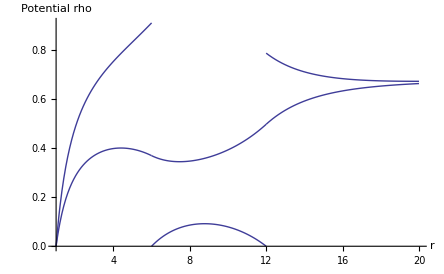

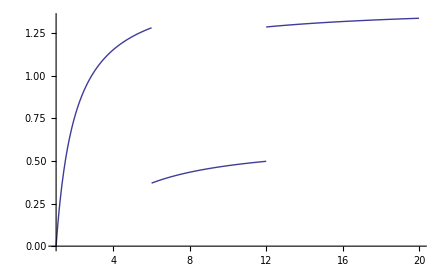

```mathematica
a = 6;
b = 12;
rs = 1;
u = 10;
x = 0.36766709138663123;
p3 = Plot[rho3[r], {r,b,20}];
p2 = Plot[rho2[r], {r,a,b}];
p1 = Plot[rho1[r], {r,rs,a}];
p7 = Plot[HeavisideTheta[r - a] - HeavisideTheta[r - b], {r,1,10}, Filling->Axis, AxesLabel->{r,Potential}];
p6 = Plot[rhom3[r], {r,b,20}];
p5 = Plot[rhom2[r], {r,a,b}];
p4 = Plot[rhom1[r], {r,rs,a}];
Show[p1,p2,p3, PlotRange -> All, AxesLabel->{r,Potential rho}]
Show[p4,p5,p6, PlotRange -> All]
```

```mathematica
a = 4.0;
b = 6.0;
rs = 1.0;
dr =0.01
u = 4.0;
x=2;
file = OpenAppend["table.txt"]
tab1 = Table[Flatten[{{r},rho1[r]}], {r,rs,a,dr}];
tab2 = Table[Flatten[{{r},rho2[r]}], {r,a,b,dr}];
tab3 = Table[Flatten[{{r},rho3[r]}], {r,b,10.0,dr}];
tab1[[All,2]] = tab1[[All,2]]/Last[tab3][[2]];
tab1[[All,3]] = tab1[[All,3]]/Last[tab3][[3]];
tab2[[All,2]] = tab2[[All,2]]/Last[tab3][[2]];
tab2[[All,3]] = tab2[[All,3]]/Last[tab3][[3]];
tab3[[All,2]] = tab3[[All,2]]/Last[tab3][[2]];
tab3[[All,3]] = tab3[[All,3]]/Last[tab3][[3]];
Last[tab3][[2]]
Export[file,tab1,"TSV"]
Export[file,tab2,"TSV"]
Export[file,tab3,"TSV"]
Close["table.txt"]
```

0.01

OutputStream[table.txt,427]

1.

OutputStream[table.txt,427]

OutputStream[table.txt,427]

OutputStream[table.txt,427]

table.txt

```mathematica
Simplify[rhodash1[rs]]
N[rhodash1[a]-invs.bcu.s.rhodash2[a]]
N[invs.bcu.s.rhodash2[b]-rhodash3[b]]
N[rhodash1'[a]-rhodash2'[a]]
N[rhodash2'[b]-rhodash3'[b]]
Simplify[rhodash3[Infinity]]
```

{{0},{0}}

{{5.55112×10^-16},{-1.11022×10^-16}}

{{1.9984×10^-15},{1.77636×10^-15}}

{{0.},{1.11022×10^-16}}

{{0.},{0.}}

{{1},{0}}

```mathematica
Total[rho1'[rs]]/Total[rho3[Infinity]]
```

{-(-91 ⅇ^20-546 ⅇ^24+1264 ⅇ^28-419 ⅇ^32+13 ⅇ^36-848 ⅇ^40-610 ⅇ^44-299 ⅇ^48)/(247 ⅇ^20-134 ⅇ^24-192 ⅇ^28-309 ⅇ^32+343 ⅇ^36+448 ⅇ^40+818 ⅇ^44+315 ⅇ^48)}